Heat

```mathematica
Clear[g,T,E0,h0,h1,sum, nF, nFlist,μmatrix,νList,νAbsList,M,denominatorlist,heatList,heat,gList,TList]
Ns=250.; (*number of atoms in state s*)
L=IntegerPart[2*Ns]; (*Length box*)
Ω=1;
m=1;
TF=1;
EF=0.;
```

```mathematica
T1=0;
T2=0.01;
T3=0.1;
```

```mathematica
g=1; (*Set coupling strength*)
T=T2;(*Set temperature*)
```

```mathematica
(*Tunnelling Hamiltonian*)
```

```mathematica
d=ConstantArray[Ω/2.,L-1];
H0=-DiagonalMatrix[d,1]-DiagonalMatrix[d,-1];
H0=ReplacePart[H0,{1,L}->-Ω/2.];
H0=ReplacePart[H0,{L,1}->-Ω/2.];

(*View as matrix*)
H0//MatrixForm;
(*Interaction Hamiltonian*)
Mp=1;
d2=Join[ConstantArray[1,Mp],ConstantArray[0,L-Mp]];
V=DiagonalMatrix[d2/Mp];
V//MatrixForm;
H1=H0+g V;
 H1//MatrixForm;

{E0,vectors0}=Eigensystem[H0];
{E1,vectors1}=Eigensystem[H1];
U0= Transpose[vectors0];
U1=Transpose[vectors1];
h0=DiagonalMatrix[E0];
h1=DiagonalMatrix[E1];

(*M Matrix*)
M=(ConjugateTranspose[U1].U0)//Chop;

μmatrix=Table[μ,{i,1,L}];

Clear[nF,nFlist,sum];

If[T==0,
nFlist={};
Do[
If[
E0[[n]]<=EF,
nFlist=Append[nFlist,1],
(*else*)
nFlist=Append[nFlist,0]
],
{n,1,L,1}];
nF=DiagonalMatrix[nFlist];
sum=Total[nFlist],

(*If nonzero temperature*)
(*h0 and μmatrix are diagonal matrices so Exp function is quicker than MatrixExp*)
denominatorlist=Exp[(E0-μmatrix)/T]+1;
sum=Total[1/denominatorlist];
(*Find chemical potential*)
μsol=FindRoot[sum==Ns ,{μ,0}];
Print[μsol];
denominatorlist=denominatorlist/.μsol;
nF=DiagonalMatrix[1/denominatorlist]
];
```

{μ→0.}

Time evolution of the correlation matrix and heat

```mathematica
dt=0.2;
tmax=100;

C0=U0.(nF.ConjugateTranspose[U0]);
energy0=Tr[H0.C0];
Vtime[t_]:=U1.(MatrixExp[-I t h1].ConjugateTranspose[U1]);

Corr[t_]:=ConjugateTranspose[Vtime[t]].(C0.Vtime[t]);
Q[t_]:=Re[Tr[H0.Corr[t]]-energy0];
heat=Table[{t,Q[t]},{t,0,tmax,dt}];
```

```mathematica
ListPlot[heat,Joined->True,PlotRange->All]
```

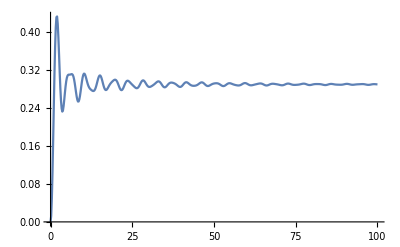

Characteristic function of heat, as function of time

```mathematica
u=0.0001; (*set counting field value*)
δt=0.5;
tmax=50;

CharFun=Table[{t,1/2+1/2(Det[IdentityMatrix[N]-nF+nF.ConjugateTranspose[M].MatrixExp[I h1 t].M.MatrixExp[I h0 u].ConjugateTranspose[M].MatrixExp[-I h1 t].M.MatrixExp[-I h0 u]])},{t,0,tmax,δt}];
```

Characteristic function of heat, as function of counting field

```mathematica
δu=0.5;
tmax=200;

CharFunTmax=Table[{u,1/2+1/2(Det[IdentityMatrix[N]-nF+nF.ConjugateTranspose[M].MatrixExp[I h1 tmax].M.MatrixExp[I h0 u].ConjugateTranspose[M].MatrixExp[-I h1 tmax].M.MatrixExp[-I h0 u]])},{u,0,300,δu}];
```

Heat from characteristic function

```mathematica
Clear[heat]
heat=Table[{CharFun[[index]][[1]],Im[CharFun[[index]][[2]]]/u},{index,1,Length[CharFun]}];
```

```mathematica
plot=ListPlot[heat,PlotStyle->{Red},Joined->True,AxesLabel->{"t","⟨Q⟩(t)"},LabelStyle->15,PlotRange->{{0,100},All}]
```